# Depression : Medicine for treatment

## depression

Depression affects 6% of adults each year and is the leading cause of suicide. The exact cause of depression is unknown.

Symptoms can be disabling and its effects pervasive

People with depression have a consistently low mood and other symptoms severe enough to interfere with normal day-to-day activities.

It can become chronic if treated inadequately

Current medications: Lithium and Imipramine

## Possible Questions:

What age group tend to be our patients?

How long have women and men been depressed?

How long were their treatments: gender matters?

Depression with treatment recurred or not?

Is there a correlation between the depression and treatment time?

What helped our patients: medication?

Was our experiment design correct?

## Importing and shaping data

Data can be obtained from the study 

Prien et al. (1984). “Drug therapy in the prevention of recurrence in unipolar and bipolar affective disorders.” published in the Archives of General Psychiatry. This dataset is a famous subset of a clinical trial conducted by the National Institute of Mental Health (NIMH) called the “Collaborative Study of the Psychobiology of Depression.” The one we will work is a simplified dataset of the original.

The file is : “depression.csv”

rawdata=Import["http://media.news.health.ufl.edu/misc/bolt/Intro/files/unit1/depression.csv"];

rawdata[[1;;7]]//TableForm

"Hospt" | "Treat" | "Outcome" | "Time" | "AcuteT" | "Age" | "Gender"
1 | "Lithium" | "Recurrence" | 36.143 | 211 | 33 | 1
1 | "Imipramine" | "No Recurrence" | 105.143 | 176 | 49 | 1
1 | "Imipramine" | "No Recurrence" | 74.571 | 191 | 50 | 1
1 | "Lithium" | "Recurrence" | 49.714 | 206 | 29 | 2
1 | "Lithium" | "No Recurrence" | 14.429 | 63 | 29 | 1
1 | "Placebo" | "Recurrence" | 5. | 70 | 30 | 2

```mathematica
rawdata;
```

```mathematica
Export["/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec9/depression.csv",rawdata]
```

/Users/murilo/Master_programs/UoA/DataScience/Lecturers/2025-2026/DataDir/Lec9/depression.csv

How our raw data looks like (briefly)

Dimensions[rawdata]

{110,7}

```mathematica
SetDirectory[]
```

/Users/murilo

Dimensions of our data

{110,7}

Time : time of treatment, it measures the long-term “wellness” period, in days. More specifically, The time until either a recurrence occurred or the study ended (censoring).

AcuteT : time patience was depressed since diagnostic and before treatment

## Data Pre-processing

Let us round up the time of treatment to full days.

```mathematica
rawdata[[2;;,4]]=Round[#]&/@rawdata[[2;;,4]]
```

{36,105,75,50,14,5,105,3,102,56,106,105,83,27,106,6,98,16,1,2,100,27,4,74,105,0,1,46,17,78,67,78,78,78,16,79,33,9,3,206,30,7,31,17,0,3,2,20,127,8,72,64,96,51,155,40,36,103,8,28,38,112,165,16,125,68,40,131,3,42,26,38,93,107,11,115,44,75,78,0,86,12,22,5,67,3,6,5,5,1,3,7,1,45,110,1,5,1,9,102,46,1,6,0,21,18,32,22,2}

Let us  replace values of gender for "female" and "male", instead of 1 and 2.

```mathematica
rawdata[[2;;,7]]=rawdata[[2;;,7]]/. 1-> "Female";
rawdata[[2;;,7]]=rawdata[[2;;,7]]/. 2-> "Male";
```

Let us transform the data into an association for further exploration, however dropping the first element of the list (“Hospt”)

```mathematica
rawdata[[1]]
```

{Hospt,Treat,Outcome,Time,AcuteT,Age,Gender}

```mathematica
keys=Drop[rawdata[[1]],1]
```

{Treat,Outcome,Time,AcuteT,Age,Gender}

We do an AssociationThred adding keys to a dataset without the first row (where the attribute names are)

```mathematica
assoc=AssociationThread[keys->#]&/@rawdata[[2;;,2;;]];
```

```mathematica
assocDS=Dataset[assoc]
```

## Data exploration and analysis

Calculate the mean age of Females

```mathematica
assocDS[Select[#Gender=="Female"&],"Age"][Mean]//N
```

41.6479

We could have done using Query:

```mathematica
Query[GroupBy[#Gender&],Mean,"Age"][assocDS]//N
```

Number of Male participants

```mathematica
assocDS[Select[#Gender=="Male"&]]//Length
```

38

Plot 2 histograms for the number of days Males and Females were depressed (“AcuteT”).

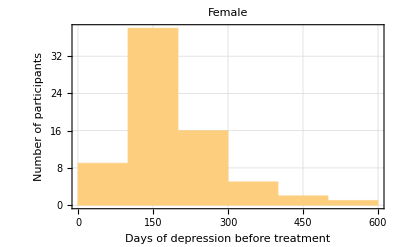
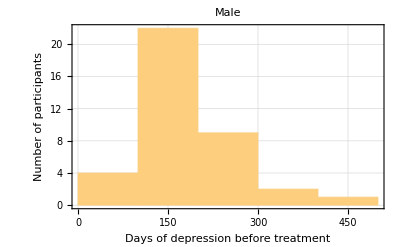

```mathematica
{Histogram[assocDS[Select[#Gender=="Female"&],"AcuteT"],PlotLabel->"Female",PlotTheme->"Detailed",FrameLabel->{"Days of depression before treatment","Number of participants"}],Histogram[assocDS[Select[#Gender=="Male"&],"AcuteT"],PlotLabel->"Male",PlotTheme->"Detailed",FrameLabel->{"Days of depression before treatment","Number of participants"}]}
```

Let us plot a graph showing treatment time ("Time") and length of being depressed ("acuteT")

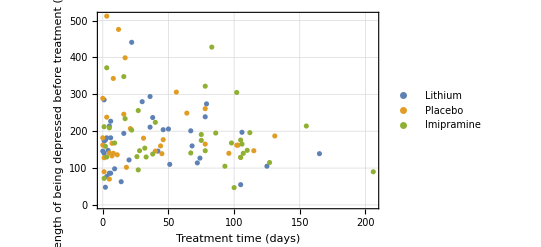

```mathematica
ListPlot[{Select[assocDS,#"Treat"=="Lithium"&][[All,3;;4]],Select[assocDS,#"Treat"=="Placebo"&][[All,3;;4]],Select[assocDS,#"Treat"=="Imipramine"&][[All,3;;4]]},PlotTheme->"Detailed",PlotLegends->{"Lithium","Placebo","Imipramine"},FrameLabel->{"Treatment time (days)","Length of being depressed before treatment (days)"}]
```

Is there a relationship between treatment time and length of being depressed before treatment?

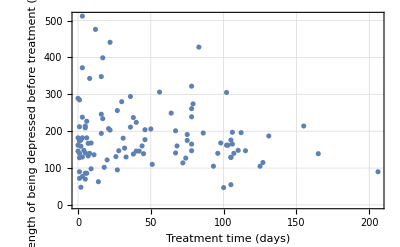

```mathematica
ListPlot[assocDS[[All,3;;4]],PlotTheme->"Detailed",FrameLabel->{"Treatment time (days)","Length of being depressed before treatment (days)"}]
```

Are these lengths correlated or anti - correlated?

```mathematica
Correlation[assocDS[All,"Time"]//Normal,assocDS[All,"AcuteT"]//Normal]//N
```

-0.127057

# Training and test data set

Let us set up the Training Set for data composed by 80 patients (eliminating Hospital Column and first row for the Key names):

```mathematica
TrainingData=RandomSample[assocDS,80];
```

The test data are the remaining group :

```mathematica
TestData=Complement[assocDS,TrainingData];
```

Let us now organize the dataset in order to put into the model. For that we have to specify the classes that we want the model to predict. In this cases, the classes are defined by the Outcome: “Recurrence” or “No Recurrence”. 

Each class has now values which the model will be built upon. Since we want to predict recurrence or not, this information cannot be part of the unknown variables. So, we need to eliminate it from the values of the classes.

Bellow None, None means that the output list is a nested list where the first level does not drop any row, the second level also does not drop any row, but the second column at level 2 is dropped .

```mathematica
GroupBy[TrainingData,#"Outcome"&]
```

```mathematica
CleanData=Drop[GroupBy[TrainingData,#"Outcome"&],None,None,{2}]
```

We might further delete unknown variables that our analysis does not count as relevant for the predicted variable . Let us say that this is the case for the AccuteT . That can be decided when for example two variables are highly correlated, only 1 needs to be taken into consideration .

We now drop the column for AccuteT:

```mathematica
CleanData1=Drop[CleanData,None,None,{3}];
```

```mathematica
CleanData1
```

```mathematica
CleanData1//Normal;
```

# Construct the model to predict recurrent or not

```mathematica
CleanData1//Normal;
```

Notice that format of dataset input in Classify is an association

```mathematica
MyModelClass=Classify[CleanData1//Normal]
```

ClassifierFunction[…]

You could have used Dataset, the format would be slightly different, entering in the Classify the data before grouping :

```mathematica
MyModelClassDATASET=Classify[TrainingData-> "Outcome"]
```

ClassifierFunction[…]

To predict if a patient will be recurrent or not, if it takes “Lithium”, time of treatment is 100, aged 60 and gender is “2”=”Male”, we can use our model :

```mathematica
MyModelClass[{"Lithium",100,60,"Male"}]
```

No Recurrence

To predict if a patient will be recurrent or not, if it takes "Placebo", time is 40, aged 60 and gender is "2"==”Male”, we can use our model :

```mathematica
MyModelClass[{"Placebo",40,60,"Male"}]
```

Recurrence

```mathematica
MyModelClass[##]&@@{{"Lithium",20,60,"Female"}}
```

Recurrence

```mathematica
MyModelClass@@{{"Lithium",20,60,"Female"}}
```

Recurrence

# Test model accuracy

We can test the accuracy of the model using the testing data.

```mathematica
Accuracy= (TP+TN)/(P+N)
```

Let us eliminate the same columns, as before:

```mathematica
CleanTestData=Drop[GroupBy[TestData,#"Outcome"&],None,None,{2}];
```

```mathematica
CleanTestData1=Drop[CleanTestData,None,None,{3}];
```

```mathematica
CleanTestData1
```

```mathematica
ClassifierMeasurements[MyModelClass,CleanTestData1//Normal, "Accuracy"]
```

0.896552

# Plot confusion matrix

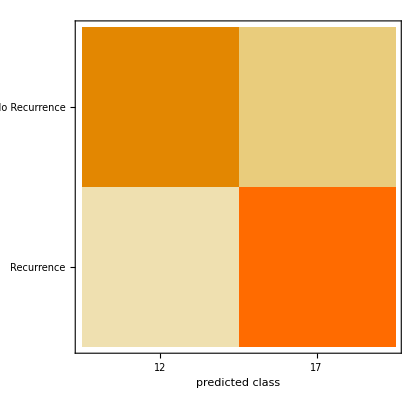

```mathematica
ClassifierMeasurements[MyModelClass,CleanTestData1//Normal,"ConfusionMatrixPlot"]
```

# ROC curve

False positive ratio (FPR), or false alarm, fall-out:  the ratio between the number of false positive (identified as positive when it is negative) and the total number of actual negative events (healthy people). You wish a small number.

Recall (or sensitivity): the ratio between the number of true positive (identified as positive when it is positive) and the total number of actual positive events (sick people). you wish a large number

```mathematica
FPR = FP/(FP+TN) 
Recall = TP/(TP+FN)
```

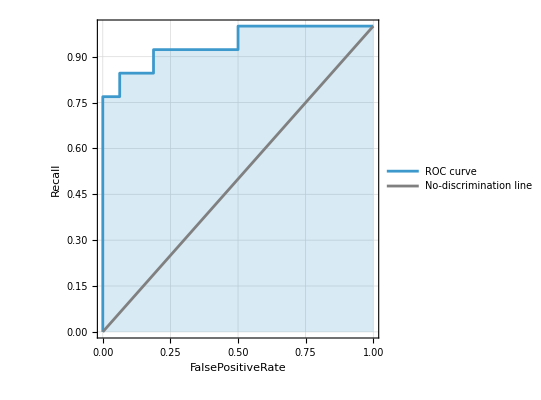
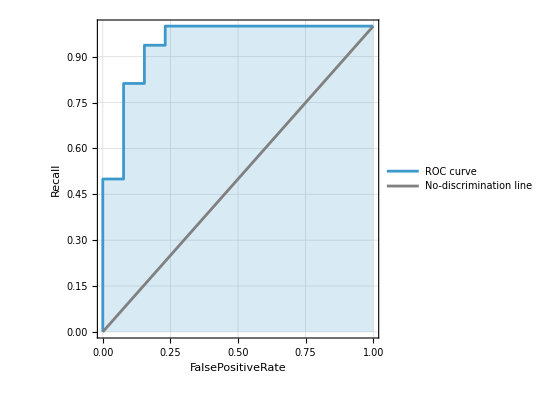
<|No Recurrence→-Graphics-,Recurrence→-Graphics-|>

```mathematica
ClassifierMeasurements[MyModelClass,CleanTestData1//Normal, "ROCCurve"]
```

Curve is created varying the threshold to which probabilities in [0, 1] are interpreted to be No Recurrence or Recurrence

## SHAP (SHapley Additive exPlanations): LInk

In Wolfram 12.3 .1, use “SHAP VALUES” to determine how important is a predictor variable to the predictability of the recurrence or no recurrence (output). They are based on the Odd Ratios.

```mathematica
MyModelClass[{"Placebo",40,60,"Female"},"SHAPValues"]
```

<|No Recurrence→<|Treat→0.982285,Time→0.660862,Age→1.05081,Gender→1.11472|>,Recurrence→<|Treat→1.01803,Time→1.51317,Age→0.951649,Gender→0.897086|>|>

```mathematica
MyModelClass[{"Lithium",100,60,2},"SHAPValues"]
```

<|No Recurrence→<|Treat→0.915095,Time→4.65153,Age→1.05081,Gender→1.12835|>,Recurrence→<|Treat→1.09278,Time→0.214983,Age→0.951649,Gender→0.886247|>|>